-4. | 108.
-3.5 | 9.45313
-3. | 0.
-2.5 | -3.79688
-2. | -16.
-1.5 | -20.6719
-1. | 0.
-0.5 | 48.8281
0. | 108.
0.5 | 144.703
1. | 128.
1.5 | 56.9531
2. | 0.
2.5 | 145.578
3. | 864.

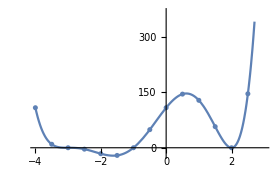
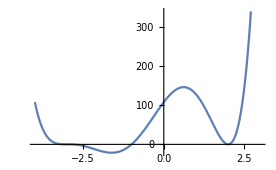
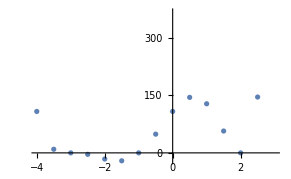
-Graphics- show[{-Graphics-}] show[{-Graphics-}]

```mathematica
a=-4;
b=3;
n=15;
h=(b-a)/(n-1);
f[x_]:=x^6+6*x^5-50*x^3-45*x^2+108*x+108
tablica = TableForm[N[Table[{x =a+i*h,f[x]},{i,0,n-1}]]]
grafik1:=ListPlot[{Table[{x =a+i*h,f[x]},{i,0,n-1}]}]
grafik2:=Plot[f[x],{x,a,b}]
show[{grafik1}]show[{grafik2}]Show[{grafik1,grafik2}]
```